# Gallery of Quantum Gates

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to use quantum gates in quantum circuits and algorithms

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package.

```mathematica
Needs["Quantum`Computing`"]
```

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## 𝒳_(q̂) Gate

The 𝒳_(q̂) gate is the first Pauli gate on qubit q. In order enter the template for this gate, press the keys:
[ESC]xg[ESC]
then press [TAB] to select the place-holder (empty square) and write the qubit number or label:

```mathematica
Subscript[𝒳, OverHat[1]]
```

𝒳_OverHat[1]

Use QuantumPlot to plot the gate in a quantum circuit:

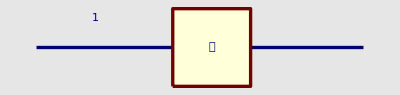

```mathematica
QuantumPlot[Subscript[𝒳, OverHat[1]]]
```

This is a more interesting circuit (Teleportation) that includes this gate:

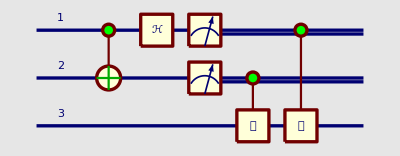

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]],{OverHat[1],OverHat[2]}],QuantumGateShifting->False]
```

This is the Dirac representation of this gate

```mathematica
QuantumEvaluate[Subscript[𝒳, OverHat[1]]]
```

|1_OverHat[1]⟩·⟨0_OverHat[1]|+|0_OverHat[1]⟩·⟨1_OverHat[1]|

This is the action of this gate on a qubit on state |0⟩

```mathematica
QuantumEvaluate[Subscript[𝒳, OverHat[1]]·|Subscript[0, OverHat[1]]⟩]
```

|1_OverHat[1]⟩

This is the action of this gate on a qubit on state |1⟩

```mathematica
QuantumEvaluate[Subscript[𝒳, OverHat[1]]·|Subscript[1, OverHat[1]]⟩]
```

|0_OverHat[1]⟩

The 𝒳[q̂] gate negates qubit q, therefore a controlled 𝒳[q̂] gate is the same as a controlled not gate (notice the use of two equal symbols == in order to indicate comparison instead of assignment):

```mathematica
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒳, OverHat[2]]]]==QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

True

This is the matrix representation of this gate:

```mathematica
QuantumMatrixForm[Subscript[𝒳, OverHat[1]]]
```

(0 | 1
1 | 0)

This is the representation of this gate in terms of Pauli operators

```mathematica
PauliExpand[Subscript[𝒳, OverHat[1]]]
```

σ_(𝒳,OverHat[1])

Products of Pauli gates are not simplified

```mathematica
Subscript[𝒳, OverHat[1]]·Subscript[𝒴, OverHat[1]]
```

𝒳_OverHat[1]·𝒴_OverHat[1]

On the other hand, products of Pauli operators are simplified

```mathematica
Subscript[σ, 𝒳,OverHat[1]]·Subscript[σ, 𝒴,OverHat[1]]
```

ⅈ σ_(𝒵,OverHat[1])

## 𝒴_(q̂) Gate

The 𝒴_(q̂) gate is the second Pauli gate on qubit q. In order enter the template for this gate, press the keys:
[ESC]yg[ESC]
then press [TAB] to select the place-holder (empty square) and write the qubit number or label:

```mathematica
Subscript[𝒴, OverHat[1]]
```

𝒴_OverHat[1]

Use QuantumPlot to plot the gate in a quantum circuit:

```mathematica
QuantumPlot[Subscript[𝒴, OverHat[1]]]
```

-Graphics-

Notice the arragenment of gates in this quantum circuit: the 𝒴 gates are in different columns in the resulting plot:

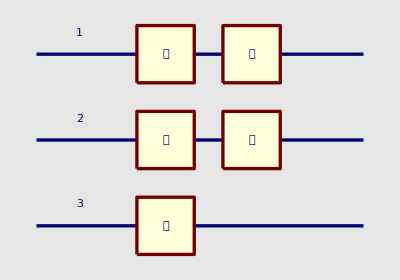

```mathematica
QuantumPlot[Subscript[𝒳, OverHat[1]]·Subscript[𝒴, OverHat[1]]·Subscript[𝒴, OverHat[2]]·Subscript[𝒴, OverHat[3]]·Subscript[𝒵, OverHat[2]]]
```

Even with the option QuantumGateShifting → False the 𝒴 gates are not in the same column

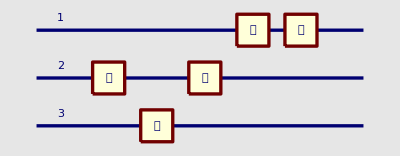

```mathematica
QuantumPlot[Subscript[𝒳, OverHat[1]]·Subscript[𝒴, OverHat[1]]·Subscript[𝒴, OverHat[2]]·Subscript[𝒴, OverHat[3]]·Subscript[𝒵, OverHat[2]],QuantumGateShifting->False]
```

There is a notation that allows to have all the 𝒴 gates in the same column. 
Press the keys [ESC]yggg[ESC] for the template:

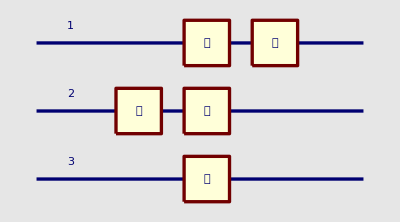

```mathematica
QuantumPlot[Subscript[𝒳, OverHat[1]]·Subscript[𝒴, {OverHat[1],OverHat[2],OverHat[3]}]·Subscript[𝒵, OverHat[2]]]
```

Both notations evaluate to the same Dirac expression:

```mathematica
QuantumEvaluate[Subscript[𝒴, OverHat[1]]·Subscript[𝒴, OverHat[2]]·Subscript[𝒴, OverHat[3]]]==QuantumEvaluate[Subscript[𝒴, {OverHat[1],OverHat[2],OverHat[3]}]]
```

True

This is the Dirac representation of this gate

```mathematica
QuantumEvaluate[Subscript[𝒴, OverHat[1]]]
```

ⅈ |1_OverHat[1]⟩·⟨0_OverHat[1]|-ⅈ |0_OverHat[1]⟩·⟨1_OverHat[1]|

This is the matrix representation of this gate:

```mathematica
QuantumMatrixForm[Subscript[𝒴, OverHat[1]]]
```

(0 | -ⅈ
ⅈ | 0)

This is the representation of this gate in terms of Pauli operators

```mathematica
PauliExpand[Subscript[𝒴, OverHat[1]]]
```

σ_(𝒴,OverHat[1])

Products of Pauli gates are not simplified

```mathematica
Subscript[𝒳, OverHat[1]]·Subscript[𝒴, OverHat[1]]
```

𝒳_OverHat[1]·𝒴_OverHat[1]

On the other hand, products of Pauli operators are simplified

```mathematica
Subscript[σ, 𝒳,OverHat[1]]·Subscript[σ, 𝒴,OverHat[1]]
```

ⅈ σ_(𝒵,OverHat[1])

## 𝒵_(q̂) Gate

The 𝒵_(q̂) gate is the third Pauli gate on qubit q. In order enter the template for this gate, press the keys:
[ESC]zg[ESC]
then press [TAB] to select the place-holder (empty square) and write the qubit number or label:

```mathematica
Subscript[𝒵, OverHat[1]]
```

𝒵_OverHat[1]

Use QuantumPlot to plot the gate in a quantum circuit:

```mathematica
QuantumPlot[Subscript[𝒵, OverHat[1]]]
```

-Graphics-

This is a more interesting circuit (Teleportation) that includes this gate:

```mathematica
QuantumPlot3D[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]],{OverHat[1],OverHat[2]}],QuantumGateShifting->False]
```

-Graphics3D-

This is the Dirac representation of this gate

```mathematica
QuantumEvaluate[Subscript[𝒵, OverHat[1]]]
```

|0_OverHat[1]⟩·⟨0_OverHat[1]|-|1_OverHat[1]⟩·⟨1_OverHat[1]|

Controlled-𝒵[q̂] gates are the same if the control qubit and the controlled qubit are exchanged
(notice the use of two equal symbols == in order to indicate comparison instead of assignment):

```mathematica
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[2]]]]==QuantumEvaluate[(𝒞^{OverHat[2]})[Subscript[𝒵, OverHat[1]]]]
```

True

Controlled-𝒵[q̂] gates are the same if the control qubit and the controlled qubit are exchanged
(notice the use of two equal symbols == in order to indicate comparison instead of assignment):

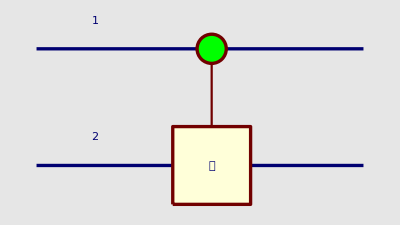
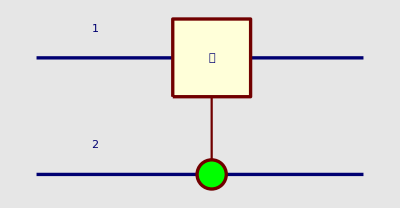
```mathematica
QuantumEvaluate[-Graphics-]==QuantumEvaluate[-Graphics-]
```

True

This is the matrix representation of this gate:

```mathematica
QuantumMatrixForm[Subscript[𝒵, OverHat[1]]]
```

(1 | 0
0 | -1)

This is the representation of this gate in terms of Pauli operators

```mathematica
PauliExpand[Subscript[𝒵, OverHat[1]]]
```

σ_(𝒵,OverHat[1])

This is the representation of a controlled-𝒵[q̂] gate in terms of Pauli operators

```mathematica
PauliExpand[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[2]]]]
```

1/2 σ_(0,OverHat[1])·σ_(0,OverHat[2])+1/2 σ_(𝒵,OverHat[1])·σ_(0,OverHat[2])+1/2 σ_(0,OverHat[1])·σ_(𝒵,OverHat[2])-1/2 σ_(𝒵,OverHat[1])·σ_(𝒵,OverHat[2])

Notice that the representation is the same if the qubits are exchanged. This is a property of controlled-𝒵[q̂] gates:

```mathematica
PauliExpand[(𝒞^{OverHat[2]})[Subscript[𝒵, OverHat[1]]]]
```

1/2 σ_(0,OverHat[1])·σ_(0,OverHat[2])+1/2 σ_(𝒵,OverHat[1])·σ_(0,OverHat[2])+1/2 σ_(0,OverHat[1])·σ_(𝒵,OverHat[2])-1/2 σ_(𝒵,OverHat[1])·σ_(𝒵,OverHat[2])

## Identity Gate ℐ_(q̂)

The ℐ_(q̂) gate is the identity gate on qubit q. In order enter the template for this gate, press the keys:
[ESC]ig[ESC]
then press [TAB] to select the place-holder (empty square) and write the qubit number or label:

```mathematica
Subscript[ℐ, OverHat[1]]
```

ℐ_OverHat[1]

The identity gate leaves the qubit without nay change

```mathematica
QuantumTableForm[Subscript[ℐ, OverHat[1]]]
```

|   Input |   Output
0 | |0_OverHat[1]⟩ | |0_OverHat[1]⟩
1 | |1_OverHat[1]⟩ | |1_OverHat[1]⟩

This is an application of the identity gate: we get the representation of the 𝒴[OverHat[2]], taking into account that qubit OverHat[1]	 also exists:

```mathematica
QuantumMatrixForm[Subscript[ℐ, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]]
```

(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

The option QubitList can be used (instead of ℐ[OverHat[1]]) in order to specify that  that qubit OverHat[1] also exists:

```mathematica
QuantumMatrixForm[Subscript[𝒴, OverHat[2]],QubitList->{OverHat[1],OverHat[2]}]
```

(0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

If neither ℐ[OverHat[1]] nor QubitList->{OverHat[1],OverHat[2]} are used, the QuantumMatrixForm assumes that OverHat[2] is the only qubit:

```mathematica
QuantumMatrixForm[Subscript[𝒴, OverHat[2]]]
```

(0 | -ⅈ
ⅈ | 0)

This is an application of the identity gate: we get the representation of the 𝒴[OverHat[2]], taking into account that qubits OverHat[1] and OverHat[3] also exists:

```mathematica
QuantumMatrixForm[Subscript[ℐ, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[ℐ, OverHat[3]]]
```

(0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0)

This is the representation of this gate in terms of Pauli operators

```mathematica
PauliExpand[Subscript[ℐ, OverHat[1]]]
```

σ_(0,OverHat[1])

Pauli gates are not simplified

```mathematica
Subscript[ℐ, OverHat[1]]·Subscript[𝒴, OverHat[1]]
```

ℐ_OverHat[1]·𝒴_OverHat[1]

On the other hand, Pauli operators are simplified

```mathematica
Subscript[σ, 0,OverHat[1]]·Subscript[σ, 𝒴,OverHat[1]]
```

σ_(𝒴,OverHat[1])

## Hadamard ℋ_(q̂) Gate

The ℋ_(q̂) gate is the Hadamard gate on qubit q. In order enter the template for this gate, press the keys:
[ESC]hg[ESC]
then press [TAB] to select the place-holder (empty square) and write the qubit number or label:

```mathematica
Subscript[ℋ, OverHat[1]]
```

ℋ_OverHat[1]

The matrix representation of the Hadamard gate:

```mathematica
QuantumMatrixForm[Subscript[ℋ, OverHat[1]]]
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

The bra-ket representation of the Hadamard gate:

```mathematica
QuantumEvaluate[Subscript[ℋ, OverHat[1]]]
```

(|0_OverHat[1]⟩·⟨0_OverHat[1]|)/(√2)+(|1_OverHat[1]⟩·⟨0_OverHat[1]|)/(√2)+(|0_OverHat[1]⟩·⟨1_OverHat[1]|)/(√2)-(|1_OverHat[1]⟩·⟨1_OverHat[1]|)/(√2)

This is the "truth table" for the Hadamard gate:

```mathematica
QuantumTableForm[Subscript[ℋ, OverHat[1]]]
```

|   Input |   Output
0 | |0_OverHat[1]⟩ | (|0_OverHat[1]⟩)/(√2)+(|1_OverHat[1]⟩)/(√2)
1 | |1_OverHat[1]⟩ | (|0_OverHat[1]⟩)/(√2)-(|1_OverHat[1]⟩)/(√2)

A Hadamard gate is usually combined with a controlled-not gate in order to generate Bell states:

```mathematica
QuantumTableForm[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | (|0_OverHat[1],0_OverHat[2]⟩)/(√2)+(|1_OverHat[1],1_OverHat[2]⟩)/(√2)
1 | |0_OverHat[1],1_OverHat[2]⟩ | (|0_OverHat[1],1_OverHat[2]⟩)/(√2)+(|1_OverHat[1],0_OverHat[2]⟩)/(√2)
2 | |1_OverHat[1],0_OverHat[2]⟩ | (|0_OverHat[1],0_OverHat[2]⟩)/(√2)-(|1_OverHat[1],1_OverHat[2]⟩)/(√2)
3 | |1_OverHat[1],1_OverHat[2]⟩ | (|0_OverHat[1],1_OverHat[2]⟩)/(√2)-(|1_OverHat[1],0_OverHat[2]⟩)/(√2)

The states generated by 𝒞^{OverHat[1]}[𝒩𝒪𝒯[OverHat[2]]]·ℋ[OverHat[1]] are the Bell states:

```mathematica
Grid[QuantumEvaluate[{{|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩},{|Subscript[ℬ, 01,OverHat[1],OverHat[2]]⟩},{|Subscript[ℬ, 10,OverHat[1],OverHat[2]]⟩},{|Subscript[ℬ, 11,OverHat[1],OverHat[2]]⟩}}],Dividers->All]
```

(|0_OverHat[1],0_OverHat[2]⟩)/(√2)+(|1_OverHat[1],1_OverHat[2]⟩)/(√2)
(|0_OverHat[1],1_OverHat[2]⟩)/(√2)+(|1_OverHat[1],0_OverHat[2]⟩)/(√2)
(|0_OverHat[1],0_OverHat[2]⟩)/(√2)-(|1_OverHat[1],1_OverHat[2]⟩)/(√2)
(|0_OverHat[1],1_OverHat[2]⟩)/(√2)-(|1_OverHat[1],0_OverHat[2]⟩)/(√2)

This is a "tensor power" of Hadamard gates:

```mathematica
(Subscript[ℋ, OverHat[1]])^(⊗3)
```

ℋ_OverHat[1]·ℋ_OverHat[2]·ℋ_OverHat[3]

Notice that the Hadamard gates are not in a column:

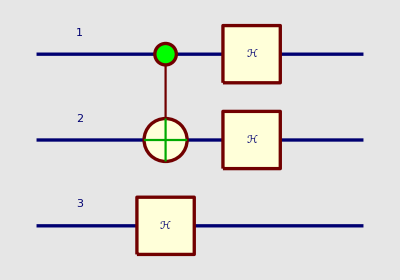

```mathematica
QuantumPlot[(Subscript[ℋ, OverHat[1]])^(⊗3)·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

Notice that the Hadamard gates are not in a column:

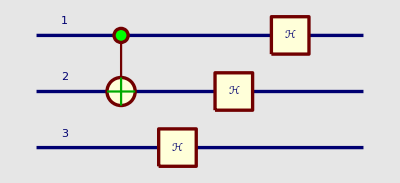

```mathematica
QuantumPlot[(Subscript[ℋ, OverHat[1]])^(⊗3)·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]],QuantumGateShifting->False]
```

There is a notation that allows to have all the ℋ gates in the same column. 
Press the keys [ESC]hggg[ESC] for the template:

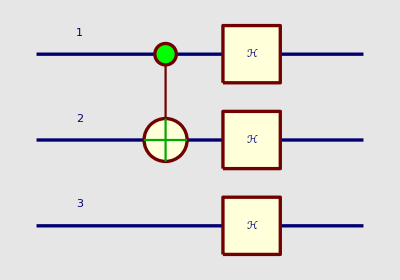

```mathematica
QuantumPlot[Subscript[ℋ, {OverHat[1],OverHat[2],OverHat[3]}]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

Both notations evaluate to the same Dirac expression:

```mathematica
QuantumEvaluate[(Subscript[ℋ, OverHat[1]])^(⊗3)]==QuantumEvaluate[Subscript[ℋ, {OverHat[1],OverHat[2],OverHat[3]}]]
```

True

This is a more interesting circuit (Teleportation) that includes this gate:

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]],{OverHat[1],OverHat[2]}],QuantumGateShifting->False]
```

-Graphics-

This is the Hadamard gate in terms of Pauli operators:

```mathematica
PauliExpand[Subscript[ℋ, OverHat[1]]]
```

(σ_(𝒳,OverHat[1]))/(√2)+(σ_(𝒵,OverHat[1]))/(√2)

## Parametric Phase Gate 𝒫_(q̂)[α]

The 𝒫_(α̂) gate is the parametric phase gate on qubit q. In order enter the template for this gate, press the keys:
[ESC]pg[ESC]
then press [TAB] to select the first place-holder (empty square) and write the qubit number or label. Press [TAB] again to select the remaining place-holder and write the parameter, for example t:

```mathematica
Subscript[𝒫, OverHat[1]][t]
```

𝒫_OverHat[1][t]

Matrix representation:

```mathematica
QuantumMatrixForm[Subscript[𝒫, OverHat[1]][t]]
```

(1 | 0
0 | ⅇ^(ⅈ t))

Dirac representation:

```mathematica
QuantumEvaluate[Subscript[𝒫, OverHat[1]][t]]
```

|0_OverHat[1]⟩·⟨0_OverHat[1]|+ⅇ^(ⅈ t) |1_OverHat[1]⟩·⟨1_OverHat[1]|

A specific value for the parameter:

```mathematica
QuantumEvaluate[Subscript[𝒫, OverHat[1]][π/4]]
```

|0_OverHat[1]⟩·⟨0_OverHat[1]|+((1+ⅈ) |1_OverHat[1]⟩·⟨1_OverHat[1]|)/(√2)

The T-π/8 gate is a particular case of the parametric phase gate:

```mathematica
Simplify[Subscript[𝒫, OverHat[1]][π/4]==Subscript[𝒯, OverHat[1]]]
```

True

The S-phase gate is another particular case of the parametric phase gate:

```mathematica
Simplify[Subscript[𝒫, OverHat[1]][π/2]==Subscript[𝒮, OverHat[1]]]
```

True

The Z-Pauli gate is another particular case of the parametric phase gate:

```mathematica
Simplify[Subscript[𝒫, OverHat[1]][π]==Subscript[𝒵, OverHat[1]]]
```

True

This simple quantum circuit can be used to generate an arbitrary superposition in a single qubit:

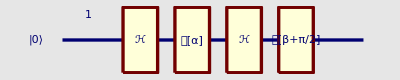

```mathematica
QuantumPlot[Subscript[𝒫, OverHat[1]][β+π/2]·Subscript[ℋ, OverHat[1]]·Subscript[𝒫, OverHat[1]][α]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]]⟩]
```

Replace QuantumPlot with QuantumEvaluate in order to "simulate" the circuit operation:

```mathematica
QuantumEvaluate[Subscript[𝒫, OverHat[1]][β+π/2]·Subscript[ℋ, OverHat[1]]·Subscript[𝒫, OverHat[1]][α]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]]⟩]
```

(1/2+ⅇ^(ⅈ α)/2) |0_OverHat[1]⟩+(1/2 ⅇ^(ⅈ (π/2+β))-1/2 ⅇ^(ⅈ α+ⅈ (π/2+β))) |1_OverHat[1]⟩

Press [ESC]pgg[ESC] to get the template that represents two phase gates with the same parameter:

```mathematica
QuantumEvaluate[Subscript[𝒫, {OverHat[1],OverHat[2]}][π/3]]
```

|0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/2 ⅈ √3 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+1/2 ⅈ √3 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|-1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+1/2 ⅈ √3 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

The two gates below, wich have the same parameter, represent the same as above:

```mathematica
QuantumEvaluate[Subscript[𝒫, OverHat[1]][π/3]·Subscript[𝒫, OverHat[2]][π/3]]
```

|0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/2 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/2 ⅈ √3 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/2 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+1/2 ⅈ √3 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|-1/2 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+1/2 ⅈ √3 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

The main use of the [ESC]pgg[ESC] template is to create circuit plots where both pahse gates are placed in the same column:

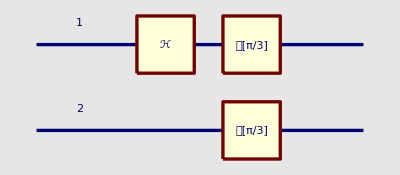
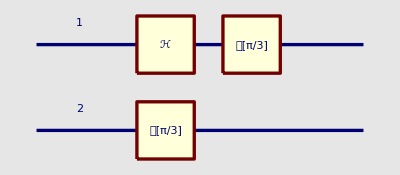

```mathematica
{QuantumPlot[Subscript[𝒫, {OverHat[1],OverHat[2]}][π/3]·Subscript[ℋ, OverHat[1]]],QuantumPlot[Subscript[𝒫, OverHat[1]][π/3]·Subscript[𝒫, OverHat[2]][π/3]·Subscript[ℋ, OverHat[1]]]}
```

The "quantum register" (press [ESC]qr[ESC]) notation has the same effect, with some advantages in the flexibility to name the qubits that make the register:

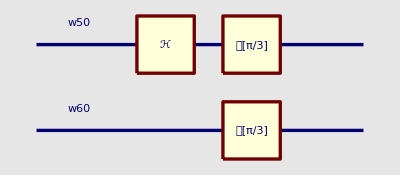
{-Graphics-,-Graphics-}

```mathematica
{QuantumPlot[Subscript[𝒫, ℛℯℊ𝒾𝓈𝓉ℯ𝓇[50,60,10,w]][π/3]·Subscript[ℋ, OverHat[w50]]],QuantumPlot[Subscript[𝒫, OverHat[1]][π/3]·Subscript[𝒫, OverHat[2]][π/3]·Subscript[ℋ, OverHat[1]]]}
```

## 𝒮_(q̂) Gate

The 𝒮_(q̂) gate is the S phase gate on qubit q. In order enter the template for this gate, press the keys:
[ESC]sg[ESC]
then press [TAB] to select the place-holder (empty square) and write the qubit number or label:

```mathematica
Subscript[𝒮, OverHat[1]]
```

𝒮_OverHat[1]

Truth-table:

```mathematica
QuantumTableForm[Subscript[𝒮, OverHat[1]]]
```

|   Input |   Output
0 | |0_OverHat[1]⟩ | |0_OverHat[1]⟩
1 | |1_OverHat[1]⟩ | ⅈ |1_OverHat[1]⟩

Matrix representation

```mathematica
QuantumMatrixForm[Subscript[𝒮, OverHat[1]]]
```

(1 | 0
0 | ⅈ)

Bra-ket representation:

```mathematica
QuantumEvaluate[Subscript[𝒮, OverHat[1]]]
```

|0_OverHat[1]⟩·⟨0_OverHat[1]|+ⅈ |1_OverHat[1]⟩·⟨1_OverHat[1]|

Gate in a circuit:

```mathematica
QuantumPlot[Subscript[𝒮, OverHat[1]]]
```

-Graphics-

This "Quantum Fourier Transform" for three qubits includes (a controlled) 𝒮 gate:

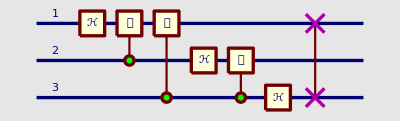

```mathematica
QuantumPlot[Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[3]]·Subscript[ℋ, OverHat[3]]·(𝒞^{OverHat[3]})[Subscript[𝒮, OverHat[2]]]·Subscript[ℋ, OverHat[2]]·(𝒞^{OverHat[3]})[Subscript[𝒯, OverHat[1]]]·(𝒞^{OverHat[2]})[Subscript[𝒮, OverHat[1]]]·Subscript[ℋ, OverHat[1]]]
```

The 𝒮_OverHat[1] gate transformed to Pauli operators.

```mathematica
PauliExpand[Subscript[𝒮, OverHat[1]]]
```

(1/2+ⅈ/2) σ_(0,OverHat[1])+(1/2-ⅈ/2) σ_(𝒵,OverHat[1])

## 𝒯_(q̂) Gate

The 𝒯_(q̂) gate is the π/8 gate on qubit q. In order enter the template for this gate, press the keys:
[ESC]tg[ESC]
then press [TAB] to select the place-holder (empty square) and write the qubit number or label:

```mathematica
Subscript[𝒯, OverHat[1]]
```

𝒯_OverHat[1]

Truth-table:

```mathematica
QuantumTableForm[Subscript[𝒯, OverHat[1]]]
```

|   Input |   Output
0 | |0_OverHat[1]⟩ | |0_OverHat[1]⟩
1 | |1_OverHat[1]⟩ | ((1+ⅈ) |1_OverHat[1]⟩)/(√2)

The fourth-power of the π/8 gate is the 𝒵_(q̂) gate:

```mathematica
{QuantumTableForm[Subscript[𝒯, OverHat[1]]^4],QuantumTableForm[Subscript[𝒵, OverHat[1]]]}
```

{ |   Input |   Output
0 | |0_OverHat[1]⟩ | |0_OverHat[1]⟩
1 | |1_OverHat[1]⟩ | -|1_OverHat[1]⟩, |   Input |   Output
0 | |0_OverHat[1]⟩ | |0_OverHat[1]⟩
1 | |1_OverHat[1]⟩ | -|1_OverHat[1]⟩}

The fourth-power of the π/8 gate is the 𝒵_(q̂) gate:

```mathematica
PauliExpand[Subscript[𝒯, OverHat[1]]^4]
```

σ_(𝒵,OverHat[1])

Matrix representation:

```mathematica
QuantumMatrixForm[Subscript[𝒯, OverHat[1]]]
```

(1 | 0
0 | (1+ⅈ)/(√2))

Numerical matrix representation:

```mathematica
N[QuantumMatrixForm[Subscript[𝒯, OverHat[1]]]]
```

(1. | 0.
0. | 0.707107+0.707107 ⅈ)

Bra-ket representation:

```mathematica
QuantumEvaluate[Subscript[𝒯, OverHat[1]]]
```

|0_OverHat[1]⟩·⟨0_OverHat[1]|+((1+ⅈ) |1_OverHat[1]⟩·⟨1_OverHat[1]|)/(√2)

This "Quantum Fourier Transform" for three qubits includes this gate. The evaluation of this command can take several seconds before showing the result:

```mathematica
QuantumTableForm[Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[3]]·Subscript[ℋ, OverHat[3]]·(𝒞^{OverHat[3]})[Subscript[𝒮, OverHat[2]]]·Subscript[ℋ, OverHat[2]]·(𝒞^{OverHat[3]})[Subscript[𝒯, OverHat[1]]]·(𝒞^{OverHat[2]})[Subscript[𝒮, OverHat[1]]]·Subscript[ℋ, OverHat[1]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(1/4+ⅈ/4) |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+(ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(1/4-ⅈ/4) |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(1/4+ⅈ/4) |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-(ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(1/4-ⅈ/4) |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(1/4-ⅈ/4) |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-(ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(1/4+ⅈ/4) |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(1/4-ⅈ/4) |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+(ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(1/4+ⅈ/4) |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(1/4+ⅈ/4) |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+(ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(1/4-ⅈ/4) |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(1/4+ⅈ/4) |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-(ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(1/4-ⅈ/4) |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | (|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(1/4-ⅈ/4) |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-(ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(1/4+ⅈ/4) |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(1/4-ⅈ/4) |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+(ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(1/4+ⅈ/4) |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩

## 𝒮𝒲𝒜𝒫_(OverHat[q1],OverHat[q2]) Gate

The 𝒮𝒲𝒜𝒫_(OverHat[q1],OverHat[q2]) gate is the swap gate on qubits q1, q2. In order enter the template for this gate, press the keys:
[ESC]swap[ESC]
then press [TAB] to select the place-holders (empty square) and write the qubit numbers or labels:

```mathematica
Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[2]]
```

𝒮𝒲𝒜𝒫_(OverHat[1],OverHat[2])

Truth table:

```mathematica
QuantumTableForm[Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[2]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | |0_OverHat[1],0_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | |1_OverHat[1],0_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | |0_OverHat[1],1_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | |1_OverHat[1],1_OverHat[2]⟩

Plot of the swap gate

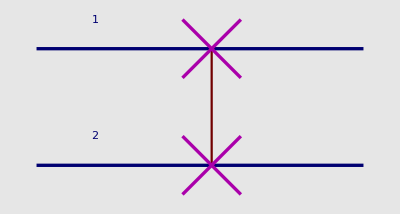

```mathematica
QuantumPlot[Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[2]]]
```

Bra-ket notation:

```mathematica
QuantumEvaluate[Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[2]]]
```

|0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+|1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+|0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+|1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

TraditionalForm Bra-ket notation:

```mathematica
TraditionalForm[QuantumEvaluate[Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[2]]]]
```

|00⟩⟨00|+|10⟩⟨01|+|01⟩⟨10|+|11⟩⟨11|

This "Quantum Fourier Transform" for three qubits includes the gate:

```mathematica
QuantumPlot3D[Subscript[𝒮𝒲𝒜𝒫, OverHat[1],OverHat[3]]·Subscript[ℋ, OverHat[3]]·(𝒞^{OverHat[3]})[Subscript[𝒮, OverHat[2]]]·Subscript[ℋ, OverHat[2]]·(𝒞^{OverHat[3]})[Subscript[𝒯, OverHat[1]]]·(𝒞^{OverHat[2]})[Subscript[𝒮, OverHat[1]]]·Subscript[ℋ, OverHat[1]]]
```

-Graphics3D-

Next circuit is equivalent to a Swap gate:

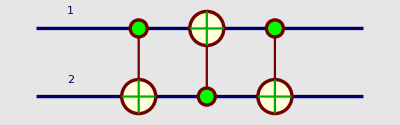

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[1]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

Next circuit is equivalent to a Swap gate:

```mathematica
QuantumEvaluate[-Graphics-]==QuantumEvaluate[-Graphics-]
```

True

## 𝒞^{OverHat[q1]}[𝒩𝒪𝒯_OverHat[q2]]Gate

The 𝒞^{OverHat[q1]}[𝒩𝒪𝒯_OverHat[q2]] gate is the control-not gate on qubits q1, q2. In order enter the template for this gate, press the keys:
[ESC]cnot[ESC]
then press [TAB] to select the place-holders (empty square) and write the qubit numbers or labels:

```mathematica
(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]
```

𝒞^{OverHat[1]}[𝒩𝒪𝒯_OverHat[2]]

The matrix representation

```mathematica
QuantumMatrixForm[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

The tensor representation

```mathematica
QuantumTensorForm[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0))

The truth table

```mathematica
QuantumTableForm[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | |0_OverHat[1],0_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | |0_OverHat[1],1_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | |1_OverHat[1],1_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | |1_OverHat[1],0_OverHat[2]⟩

Next circuit is equivalent to a Swap gate:

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[1]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

-Graphics-

Next circuit is equivalent to a Swap gate:

```mathematica
QuantumTableForm[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[1]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | |0_OverHat[1],0_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | |1_OverHat[1],0_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | |0_OverHat[1],1_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | |1_OverHat[1],1_OverHat[2]⟩

## 𝒯𝒪ℱℱ𝒪ℒℐ_(OverHat[q1],OverHat[q2],OverHat[q3]) Gate

The 𝒯𝒪ℱℱ𝒪ℒℐ_(OverHat[q1],OverHat[q2],OverHat[q3]) gate is the Toffoli gate (control-control-not) on qubits q1, q2, q3. In order enter the template for this gate, press the keys:
[ESC]toff[ESC]
then press [TAB] to select the place-holders (empty square) and write the qubit numbers or labels:

```mathematica
Subscript[𝒯𝒪ℱℱ𝒪ℒℐ, OverHat[1],OverHat[2],OverHat[3]]
```

𝒞^{OverHat[1],OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]

A Toffoli gate is actually a control-contol-not:

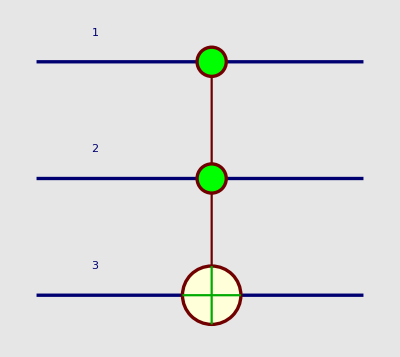

```mathematica
QuantumPlot[Subscript[𝒯𝒪ℱℱ𝒪ℒℐ, OverHat[1],OverHat[2],OverHat[3]]]
```

Truth table:

```mathematica
QuantumTableForm[Subscript[𝒯𝒪ℱℱ𝒪ℒℐ, OverHat[1],OverHat[2],OverHat[3]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩

This is the Toffoli gate in terms of Pauli operators:

```mathematica
PauliExpand[Subscript[𝒯𝒪ℱℱ𝒪ℒℐ, OverHat[1],OverHat[2],OverHat[3]]]
```

3/4 σ_(0,OverHat[1])·σ_(0,OverHat[2])·σ_(0,OverHat[3])+1/4 σ_(𝒵,OverHat[1])·σ_(0,OverHat[2])·σ_(0,OverHat[3])+1/4 σ_(0,OverHat[1])·σ_(𝒵,OverHat[2])·σ_(0,OverHat[3])-1/4 σ_(𝒵,OverHat[1])·σ_(𝒵,OverHat[2])·σ_(0,OverHat[3])+1/4 σ_(0,OverHat[1])·σ_(0,OverHat[2])·σ_(𝒳,OverHat[3])-1/4 σ_(𝒵,OverHat[1])·σ_(0,OverHat[2])·σ_(𝒳,OverHat[3])-1/4 σ_(0,OverHat[1])·σ_(𝒵,OverHat[2])·σ_(𝒳,OverHat[3])+1/4 σ_(𝒵,OverHat[1])·σ_(𝒵,OverHat[2])·σ_(𝒳,OverHat[3])

## ℱℛℰ𝒟𝒦ℐ𝒩_(OverHat[q1],OverHat[q2],OverHat[q3]) Gate

The ℱℛℰ𝒟𝒦ℐ𝒩_(OverHat[q1],OverHat[q2],OverHat[q3]) gate is the Fredkin gate (control-swap) on qubits q1, q2, q3. In order enter the template for this gate, press the keys:
[ESC]fred[ESC]
then press [TAB] to select the place-holders (empty square) and write the qubit numbers or labels:

```mathematica
Subscript[ℱℛℰ𝒟𝒦ℐ𝒩, OverHat[1],OverHat[2],OverHat[3]]
```

𝒞^{OverHat[1]}[𝒮𝒲𝒜𝒫_(OverHat[2],OverHat[3])]

A Fredkin gate is actually a control-swap:

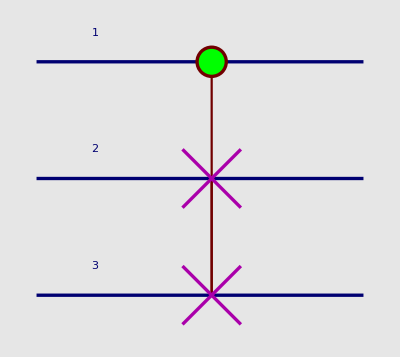

```mathematica
QuantumPlot[Subscript[ℱℛℰ𝒟𝒦ℐ𝒩, OverHat[1],OverHat[2],OverHat[3]]]
```

Truth table:

```mathematica
QuantumTableForm[Subscript[ℱℛℰ𝒟𝒦ℐ𝒩, OverHat[1],OverHat[2],OverHat[3]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩

This is the Toffoli gate in terms of Pauli operators:

```mathematica
PauliExpand[Subscript[ℱℛℰ𝒟𝒦ℐ𝒩, OverHat[1],OverHat[2],OverHat[3]]]
```

3/4 σ_(0,OverHat[1])·σ_(0,OverHat[2])·σ_(0,OverHat[3])+1/4 σ_(𝒵,OverHat[1])·σ_(0,OverHat[2])·σ_(0,OverHat[3])+1/4 σ_(0,OverHat[1])·σ_(𝒳,OverHat[2])·σ_(𝒳,OverHat[3])-1/4 σ_(𝒵,OverHat[1])·σ_(𝒳,OverHat[2])·σ_(𝒳,OverHat[3])+1/4 σ_(0,OverHat[1])·σ_(𝒴,OverHat[2])·σ_(𝒴,OverHat[3])-1/4 σ_(𝒵,OverHat[1])·σ_(𝒴,OverHat[2])·σ_(𝒴,OverHat[3])+1/4 σ_(0,OverHat[1])·σ_(𝒵,OverHat[2])·σ_(𝒵,OverHat[3])-1/4 σ_(𝒵,OverHat[1])·σ_(𝒵,OverHat[2])·σ_(𝒵,OverHat[3])

TraditionalForm gives a format closer to the format used in papers and textbooks:

```mathematica
TraditionalForm[PauliExpand[Subscript[ℱℛℰ𝒟𝒦ℐ𝒩, OverHat[1],OverHat[2],OverHat[3]]]]
```

-1/4 σ_1^𝒵σ_2^𝒳σ_3^𝒳+1/4 σ_1^0σ_2^𝒳σ_3^𝒳-1/4 σ_1^𝒵σ_2^𝒴σ_3^𝒴+1/4 σ_1^0σ_2^𝒴σ_3^𝒴+1/4 σ_1^𝒵σ_2^0σ_3^0+1/4 σ_1^0σ_2^𝒵σ_3^𝒵-1/4 σ_1^𝒵σ_2^𝒵σ_3^𝒵+3/4 σ_1^0σ_2^0σ_3^0

## Controlled Gates

Truth table for an arbitrary controlled-gate. Press [ESC]cgate[ESC] for the controlled-gate template 𝒞^{OverHat[□]}[□] and [ESC]qg[ESC] for the quantum gate template □_OverHat[□]:

```mathematica
SetQuantumGate[mygate,1];
QuantumTableForm[(𝒞^{OverHat[1]})[Subscript[mygate, OverHat[2]]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | |0_OverHat[1],0_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | |0_OverHat[1],1_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | |1_OverHat[1]⟩·mygate_OverHat[2]·|0_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | |1_OverHat[1]⟩·mygate_OverHat[2]·|1_OverHat[2]⟩

Matrix representation for an arbitrary controlled-gate. Press [ESC]cgate[ESC] for the controlled-gate template:

```mathematica
SetQuantumGate[mygate,1];
QuantumMatrixForm[(𝒞^{OverHat[1]})[Subscript[mygate, OverHat[2]]]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⟨0_OverHat[2]|·mygate_OverHat[2]·|0_OverHat[2]⟩ | ⟨0_OverHat[2]|·mygate_OverHat[2]·|1_OverHat[2]⟩
0 | 0 | ⟨1_OverHat[2]|·mygate_OverHat[2]·|0_OverHat[2]⟩ | ⟨1_OverHat[2]|·mygate_OverHat[2]·|1_OverHat[2]⟩)

Bra-ket representation for an arbitrary controlled-gate. Press [ESC]cgate[ESC] for the controlled-gate template:

```mathematica
SetQuantumGate[mygate,1];
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[mygate, OverHat[2]]]]
```

|0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+|0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+|1_OverHat[1]⟩·mygate_OverHat[2]·⟨1_OverHat[1]|

## Quantum Fourier Transform 𝒬ℱ𝒯

Press [ESC]qft[ESC] for the template of the one-qubit Quantum Fourier Transform

```mathematica
Subscript[𝒬ℱ𝒯, OverHat[1]]
```

𝒬ℱ𝒯_OverHat[1]

Its truth table:

```mathematica
QuantumTableForm[Subscript[𝒬ℱ𝒯, OverHat[1]]]
```

|   Input |   Output
0 | |0_OverHat[1]⟩ | 0.707107 |0_OverHat[1]⟩+0.707107 |1_OverHat[1]⟩
1 | |1_OverHat[1]⟩ | 0.707107 |0_OverHat[1]⟩-0.707107 |1_OverHat[1]⟩

Press [ESC]qqft[ESC] for the template of the two-qubits Quantum Fourier Transform. Scroll to the right in order to see the full answer:

```mathematica
QuantumTableForm[Subscript[𝒬ℱ𝒯, OverHat[1],OverHat[2]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2]⟩ | 0.5 |0_OverHat[1],0_OverHat[2]⟩+0.5 |0_OverHat[1],1_OverHat[2]⟩+0.5 |1_OverHat[1],0_OverHat[2]⟩+0.5 |1_OverHat[1],1_OverHat[2]⟩
1 | |0_OverHat[1],1_OverHat[2]⟩ | 0.5 |0_OverHat[1],0_OverHat[2]⟩+0.5 ⅈ |0_OverHat[1],1_OverHat[2]⟩-0.5 |1_OverHat[1],0_OverHat[2]⟩-0.5 ⅈ |1_OverHat[1],1_OverHat[2]⟩
2 | |1_OverHat[1],0_OverHat[2]⟩ | 0.5 |0_OverHat[1],0_OverHat[2]⟩-0.5 |0_OverHat[1],1_OverHat[2]⟩+0.5 |1_OverHat[1],0_OverHat[2]⟩-0.5 |1_OverHat[1],1_OverHat[2]⟩
3 | |1_OverHat[1],1_OverHat[2]⟩ | 0.5 |0_OverHat[1],0_OverHat[2]⟩-0.5 ⅈ |0_OverHat[1],1_OverHat[2]⟩-0.5 |1_OverHat[1],0_OverHat[2]⟩+0.5 ⅈ |1_OverHat[1],1_OverHat[2]⟩

The Hermitian Conjugate of any gate is its inverse, because by definition all gates are unitary (they preserve the norm of the state kets). Therefore, the Hermitian of the Quantum Fourier Transform is the inverserse transform, as you can see by comparing the result of the calculation below with the last row of the table above. Press [ESC]her[ESC] for the Hermitian Conjugate template (□)^†, and press [ESC]qqft[ESC] for the template of the two-qubits Quantum Fourier Transform 𝒬ℱ𝒯_(OverHat[□],OverHat[□]):

```mathematica
QuantumEvaluate[SuperDagger[(Subscript[𝒬ℱ𝒯, OverHat[1],OverHat[2]])]·(1/2 |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩-1/2 ⅈ |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩-
1/2 |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+1/2 ⅈ |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩)]
```

(0.+0. ⅈ) |0_OverHat[1],0_OverHat[2]⟩+0. |0_OverHat[1],1_OverHat[2]⟩+(0.+0. ⅈ) |1_OverHat[1],0_OverHat[2]⟩+1. |1_OverHat[1],1_OverHat[2]⟩

Chop replaces approximate real numbers in expr that are close to zero by the exact integer 0:

```mathematica
Chop[QuantumEvaluate[SuperDagger[(Subscript[𝒬ℱ𝒯, OverHat[1],OverHat[2]])]·(1/2 |Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩-1/2 ⅈ |Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩-
1/2 |Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+1/2 ⅈ |Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩)]]
```

1. |1_OverHat[1],1_OverHat[2]⟩

Press [ESC]qqqft[ESC] for the template of the three-qubits Quantum Fourier Transform. Scroll to the right in order to see the full answer:

```mathematica
QuantumTableForm[Subscript[𝒬ℱ𝒯, OverHat[1],OverHat[2],OverHat[3]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | 0.353553 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+0.353553 |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+0.353553 |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+0.353553 |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩+0.353553 |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+0.353553 |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+0.353553 |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+0.353553 |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
1 | |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | 0.353553 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+(0.25+0.25 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+0.353553 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩-(0.25-0.25 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩-0.353553 |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩-(0.25+0.25 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-0.353553 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+(0.25-0.25 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
2 | |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | 0.353553 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+0.353553 ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-0.353553 |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩-0.353553 ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩+0.353553 |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+0.353553 ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-0.353553 |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩-0.353553 ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
3 | |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | 0.353553 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩-(0.25-0.25 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-0.353553 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+(0.25+0.25 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩-0.353553 |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+(0.25-0.25 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+0.353553 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩-(0.25+0.25 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
4 | |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩ | 0.353553 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩-0.353553 |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+0.353553 |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩-0.353553 |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩+0.353553 |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩-0.353553 |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+0.353553 |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩-0.353553 |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
5 | |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩ | 0.353553 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩-(0.25+0.25 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+0.353553 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+(0.25-0.25 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩-0.353553 |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+(0.25+0.25 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-0.353553 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩-(0.25-0.25 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
6 | |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩ | 0.353553 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩-0.353553 ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-0.353553 |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+0.353553 ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩+0.353553 |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩-0.353553 ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-0.353553 |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+0.353553 ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩
7 | |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩ | 0.353553 |0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+(0.25-0.25 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩-0.353553 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩-(0.25+0.25 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩-0.353553 |1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩-(0.25-0.25 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩+0.353553 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩+(0.25+0.25 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩

Press [ESC]qqqqft[ESC] for the template of the four-qubits Quantum Fourier Transform. Scroll to the right in order to see the full answer:

```mathematica
QuantumTableForm[Subscript[𝒬ℱ𝒯, OverHat[1],OverHat[2],OverHat[3],OverHat[4]]]
```

|   Input |   Output
0 | |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+0.25 |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+0.25 |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+0.25 |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
1 | |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.23097+0.0956709 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.0956709+0.23097 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.0956709-0.23097 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.23097-0.0956709 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.23097+0.0956709 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.0956709+0.23097 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.0956709-0.23097 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.23097-0.0956709 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
2 | |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
3 | |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.0956709+0.23097 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.23097+0.0956709 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.23097-0.0956709 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.0956709-0.23097 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.0956709+0.23097 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.23097+0.0956709 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.23097-0.0956709 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.0956709-0.23097 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
4 | |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
5 | |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.0956709-0.23097 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.23097-0.0956709 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.23097+0.0956709 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.0956709+0.23097 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.0956709-0.23097 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.23097-0.0956709 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.23097+0.0956709 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.0956709+0.23097 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
6 | |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
7 | |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.23097-0.0956709 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.0956709-0.23097 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.0956709+0.23097 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.23097+0.0956709 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.23097-0.0956709 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.0956709-0.23097 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.0956709+0.23097 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.23097+0.0956709 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
8 | |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-0.25 |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-0.25 |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-0.25 |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
9 | |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.23097+0.0956709 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.0956709+0.23097 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.0956709-0.23097 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.23097-0.0956709 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.23097+0.0956709 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.0956709+0.23097 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.0956709-0.23097 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.23097-0.0956709 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
10 | |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
11 | |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.0956709+0.23097 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.23097+0.0956709 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.23097-0.0956709 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.0956709-0.23097 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.0956709+0.23097 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.23097+0.0956709 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.23097-0.0956709 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.0956709-0.23097 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
12 | |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
13 | |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.0956709-0.23097 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.23097-0.0956709 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.23097+0.0956709 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.0956709+0.23097 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.0956709-0.23097 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.23097-0.0956709 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.23097+0.0956709 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.0956709+0.23097 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
14 | |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩
15 | |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩ | 0.25 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.23097-0.0956709 ⅈ) |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777-0.176777 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.0956709-0.23097 ⅈ) |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 ⅈ |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.0956709+0.23097 ⅈ) |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777+0.176777 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.23097+0.0956709 ⅈ) |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-0.25 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-(0.23097-0.0956709 ⅈ) |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-(0.176777-0.176777 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-(0.0956709-0.23097 ⅈ) |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.25 ⅈ |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+(0.0956709+0.23097 ⅈ) |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+(0.176777+0.176777 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+(0.23097+0.0956709 ⅈ) |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩

TraditionalForm gives a format closer to the format used in papers and textbooks.  Scroll to the right in order to see the full answer:

```mathematica
TraditionalForm[QuantumTableForm[Subscript[𝒬ℱ𝒯, OverHat[1],OverHat[2],OverHat[3],OverHat[4]]]]
```

|   Input |   Output
0 | |0000⟩ | 0.25 |0000⟩+0.25 |0001⟩+0.25 |0010⟩+0.25 |0011⟩+0.25 |0100⟩+0.25 |0101⟩+0.25 |0110⟩+0.25 |0111⟩+0.25 |1000⟩+0.25 |1001⟩+0.25 |1010⟩+0.25 |1011⟩+0.25 |1100⟩+0.25 |1101⟩+0.25 |1110⟩+0.25 |1111⟩
1 | |0001⟩ | 0.25 |0000⟩+(0.23097+0.0956709 ⅈ) |0001⟩+(0.176777+0.176777 ⅈ) |0010⟩+(0.0956709+0.23097 ⅈ) |0011⟩+0.25 ⅈ |0100⟩-(0.0956709-0.23097 ⅈ) |0101⟩-(0.176777-0.176777 ⅈ) |0110⟩-(0.23097-0.0956709 ⅈ) |0111⟩-0.25 |1000⟩-(0.23097+0.0956709 ⅈ) |1001⟩-(0.176777+0.176777 ⅈ) |1010⟩-(0.0956709+0.23097 ⅈ) |1011⟩-0.25 ⅈ |1100⟩+(0.0956709-0.23097 ⅈ) |1101⟩+(0.176777-0.176777 ⅈ) |1110⟩+(0.23097-0.0956709 ⅈ) |1111⟩
2 | |0010⟩ | 0.25 |0000⟩+(0.176777+0.176777 ⅈ) |0001⟩+0.25 ⅈ |0010⟩-(0.176777-0.176777 ⅈ) |0011⟩-0.25 |0100⟩-(0.176777+0.176777 ⅈ) |0101⟩-0.25 ⅈ |0110⟩+(0.176777-0.176777 ⅈ) |0111⟩+0.25 |1000⟩+(0.176777+0.176777 ⅈ) |1001⟩+0.25 ⅈ |1010⟩-(0.176777-0.176777 ⅈ) |1011⟩-0.25 |1100⟩-(0.176777+0.176777 ⅈ) |1101⟩-0.25 ⅈ |1110⟩+(0.176777-0.176777 ⅈ) |1111⟩
3 | |0011⟩ | 0.25 |0000⟩+(0.0956709+0.23097 ⅈ) |0001⟩-(0.176777-0.176777 ⅈ) |0010⟩-(0.23097+0.0956709 ⅈ) |0011⟩-0.25 ⅈ |0100⟩+(0.23097-0.0956709 ⅈ) |0101⟩+(0.176777+0.176777 ⅈ) |0110⟩-(0.0956709-0.23097 ⅈ) |0111⟩-0.25 |1000⟩-(0.0956709+0.23097 ⅈ) |1001⟩+(0.176777-0.176777 ⅈ) |1010⟩+(0.23097+0.0956709 ⅈ) |1011⟩+0.25 ⅈ |1100⟩-(0.23097-0.0956709 ⅈ) |1101⟩-(0.176777+0.176777 ⅈ) |1110⟩+(0.0956709-0.23097 ⅈ) |1111⟩
4 | |0100⟩ | 0.25 |0000⟩+0.25 ⅈ |0001⟩-0.25 |0010⟩-0.25 ⅈ |0011⟩+0.25 |0100⟩+0.25 ⅈ |0101⟩-0.25 |0110⟩-0.25 ⅈ |0111⟩+0.25 |1000⟩+0.25 ⅈ |1001⟩-0.25 |1010⟩-0.25 ⅈ |1011⟩+0.25 |1100⟩+0.25 ⅈ |1101⟩-0.25 |1110⟩-0.25 ⅈ |1111⟩
5 | |0101⟩ | 0.25 |0000⟩-(0.0956709-0.23097 ⅈ) |0001⟩-(0.176777+0.176777 ⅈ) |0010⟩+(0.23097-0.0956709 ⅈ) |0011⟩+0.25 ⅈ |0100⟩-(0.23097+0.0956709 ⅈ) |0101⟩+(0.176777-0.176777 ⅈ) |0110⟩+(0.0956709+0.23097 ⅈ) |0111⟩-0.25 |1000⟩+(0.0956709-0.23097 ⅈ) |1001⟩+(0.176777+0.176777 ⅈ) |1010⟩-(0.23097-0.0956709 ⅈ) |1011⟩-0.25 ⅈ |1100⟩+(0.23097+0.0956709 ⅈ) |1101⟩-(0.176777-0.176777 ⅈ) |1110⟩-(0.0956709+0.23097 ⅈ) |1111⟩
6 | |0110⟩ | 0.25 |0000⟩-(0.176777-0.176777 ⅈ) |0001⟩-0.25 ⅈ |0010⟩+(0.176777+0.176777 ⅈ) |0011⟩-0.25 |0100⟩+(0.176777-0.176777 ⅈ) |0101⟩+0.25 ⅈ |0110⟩-(0.176777+0.176777 ⅈ) |0111⟩+0.25 |1000⟩-(0.176777-0.176777 ⅈ) |1001⟩-0.25 ⅈ |1010⟩+(0.176777+0.176777 ⅈ) |1011⟩-0.25 |1100⟩+(0.176777-0.176777 ⅈ) |1101⟩+0.25 ⅈ |1110⟩-(0.176777+0.176777 ⅈ) |1111⟩
7 | |0111⟩ | 0.25 |0000⟩-(0.23097-0.0956709 ⅈ) |0001⟩+(0.176777-0.176777 ⅈ) |0010⟩-(0.0956709-0.23097 ⅈ) |0011⟩-0.25 ⅈ |0100⟩+(0.0956709+0.23097 ⅈ) |0101⟩-(0.176777+0.176777 ⅈ) |0110⟩+(0.23097+0.0956709 ⅈ) |0111⟩-0.25 |1000⟩+(0.23097-0.0956709 ⅈ) |1001⟩-(0.176777-0.176777 ⅈ) |1010⟩+(0.0956709-0.23097 ⅈ) |1011⟩+0.25 ⅈ |1100⟩-(0.0956709+0.23097 ⅈ) |1101⟩+(0.176777+0.176777 ⅈ) |1110⟩-(0.23097+0.0956709 ⅈ) |1111⟩
8 | |1000⟩ | 0.25 |0000⟩-0.25 |0001⟩+0.25 |0010⟩-0.25 |0011⟩+0.25 |0100⟩-0.25 |0101⟩+0.25 |0110⟩-0.25 |0111⟩+0.25 |1000⟩-0.25 |1001⟩+0.25 |1010⟩-0.25 |1011⟩+0.25 |1100⟩-0.25 |1101⟩+0.25 |1110⟩-0.25 |1111⟩
9 | |1001⟩ | 0.25 |0000⟩-(0.23097+0.0956709 ⅈ) |0001⟩+(0.176777+0.176777 ⅈ) |0010⟩-(0.0956709+0.23097 ⅈ) |0011⟩+0.25 ⅈ |0100⟩+(0.0956709-0.23097 ⅈ) |0101⟩-(0.176777-0.176777 ⅈ) |0110⟩+(0.23097-0.0956709 ⅈ) |0111⟩-0.25 |1000⟩+(0.23097+0.0956709 ⅈ) |1001⟩-(0.176777+0.176777 ⅈ) |1010⟩+(0.0956709+0.23097 ⅈ) |1011⟩-0.25 ⅈ |1100⟩-(0.0956709-0.23097 ⅈ) |1101⟩+(0.176777-0.176777 ⅈ) |1110⟩-(0.23097-0.0956709 ⅈ) |1111⟩
10 | |1010⟩ | 0.25 |0000⟩-(0.176777+0.176777 ⅈ) |0001⟩+0.25 ⅈ |0010⟩+(0.176777-0.176777 ⅈ) |0011⟩-0.25 |0100⟩+(0.176777+0.176777 ⅈ) |0101⟩-0.25 ⅈ |0110⟩-(0.176777-0.176777 ⅈ) |0111⟩+0.25 |1000⟩-(0.176777+0.176777 ⅈ) |1001⟩+0.25 ⅈ |1010⟩+(0.176777-0.176777 ⅈ) |1011⟩-0.25 |1100⟩+(0.176777+0.176777 ⅈ) |1101⟩-0.25 ⅈ |1110⟩-(0.176777-0.176777 ⅈ) |1111⟩
11 | |1011⟩ | 0.25 |0000⟩-(0.0956709+0.23097 ⅈ) |0001⟩-(0.176777-0.176777 ⅈ) |0010⟩+(0.23097+0.0956709 ⅈ) |0011⟩-0.25 ⅈ |0100⟩-(0.23097-0.0956709 ⅈ) |0101⟩+(0.176777+0.176777 ⅈ) |0110⟩+(0.0956709-0.23097 ⅈ) |0111⟩-0.25 |1000⟩+(0.0956709+0.23097 ⅈ) |1001⟩+(0.176777-0.176777 ⅈ) |1010⟩-(0.23097+0.0956709 ⅈ) |1011⟩+0.25 ⅈ |1100⟩+(0.23097-0.0956709 ⅈ) |1101⟩-(0.176777+0.176777 ⅈ) |1110⟩-(0.0956709-0.23097 ⅈ) |1111⟩
12 | |1100⟩ | 0.25 |0000⟩-0.25 ⅈ |0001⟩-0.25 |0010⟩+0.25 ⅈ |0011⟩+0.25 |0100⟩-0.25 ⅈ |0101⟩-0.25 |0110⟩+0.25 ⅈ |0111⟩+0.25 |1000⟩-0.25 ⅈ |1001⟩-0.25 |1010⟩+0.25 ⅈ |1011⟩+0.25 |1100⟩-0.25 ⅈ |1101⟩-0.25 |1110⟩+0.25 ⅈ |1111⟩
13 | |1101⟩ | 0.25 |0000⟩+(0.0956709-0.23097 ⅈ) |0001⟩-(0.176777+0.176777 ⅈ) |0010⟩-(0.23097-0.0956709 ⅈ) |0011⟩+0.25 ⅈ |0100⟩+(0.23097+0.0956709 ⅈ) |0101⟩+(0.176777-0.176777 ⅈ) |0110⟩-(0.0956709+0.23097 ⅈ) |0111⟩-0.25 |1000⟩-(0.0956709-0.23097 ⅈ) |1001⟩+(0.176777+0.176777 ⅈ) |1010⟩+(0.23097-0.0956709 ⅈ) |1011⟩-0.25 ⅈ |1100⟩-(0.23097+0.0956709 ⅈ) |1101⟩-(0.176777-0.176777 ⅈ) |1110⟩+(0.0956709+0.23097 ⅈ) |1111⟩
14 | |1110⟩ | 0.25 |0000⟩+(0.176777-0.176777 ⅈ) |0001⟩-0.25 ⅈ |0010⟩-(0.176777+0.176777 ⅈ) |0011⟩-0.25 |0100⟩-(0.176777-0.176777 ⅈ) |0101⟩+0.25 ⅈ |0110⟩+(0.176777+0.176777 ⅈ) |0111⟩+0.25 |1000⟩+(0.176777-0.176777 ⅈ) |1001⟩-0.25 ⅈ |1010⟩-(0.176777+0.176777 ⅈ) |1011⟩-0.25 |1100⟩-(0.176777-0.176777 ⅈ) |1101⟩+0.25 ⅈ |1110⟩+(0.176777+0.176777 ⅈ) |1111⟩
15 | |1111⟩ | 0.25 |0000⟩+(0.23097-0.0956709 ⅈ) |0001⟩+(0.176777-0.176777 ⅈ) |0010⟩+(0.0956709-0.23097 ⅈ) |0011⟩-0.25 ⅈ |0100⟩-(0.0956709+0.23097 ⅈ) |0101⟩-(0.176777+0.176777 ⅈ) |0110⟩-(0.23097+0.0956709 ⅈ) |0111⟩-0.25 |1000⟩-(0.23097-0.0956709 ⅈ) |1001⟩-(0.176777-0.176777 ⅈ) |1010⟩-(0.0956709-0.23097 ⅈ) |1011⟩+0.25 ⅈ |1100⟩+(0.0956709+0.23097 ⅈ) |1101⟩+(0.176777+0.176777 ⅈ) |1110⟩+(0.23097+0.0956709 ⅈ) |1111⟩

by José Luis Gómez-Muñoz 
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx